## Day 4

### Problem 2 (problem 1 is exactly the same with different well potential

```mathematica
a = 5;
ϕ[x_,n_]= Sqrt[2/a] Sin[n Pi x/a];
```

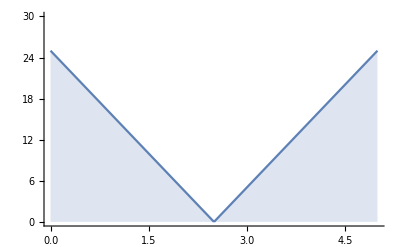

```mathematica
v0=25;
v1 = 0;w0=3;w1=5;
Plot[Which[x<a/2,v0(1-2  x/a),x<a,v0(2x/a-1),True,100000],{x,0,a},Filling->Bottom,FillingStyle->{Blue,Opacity[.2]},PlotRange->{All,{0,30}}]

V[n_,m_] := Integrate[ϕ[x,m,a] v0(1-2  x/a) ϕ[x,n,a],{x,0,a/2}]+Integrate[ϕ[x,m,a] v0(2x/a-1) ϕ[x,n,a],{x,a/2,a}]
K[n_] := -Integrate[ϕ[x,n,a] D[ϕ[x,n,a],{x,2}],{x,0,a}]
```

20

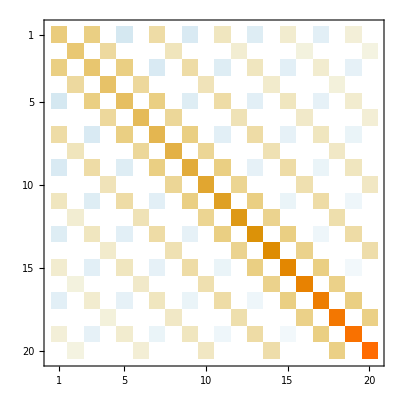

```mathematica
nBasis = 20;
Hmat = ConstantArray[0,{nBasis,nBasis}];
Table[V[n,m],{n,1,nBasis},{m,1,nBasis}];
Hmat = Hmat + %;
MatrixPlot[Hmat];
DiagonalMatrix[Table[K[n],{n,1,nBasis}]]//N;
Hmat = Hmat + %;
MatrixPlot[Hmat]
```

```mathematica
{eigvals,eigvecs}= Eigensystem[Hmat];
```

```mathematica
idx=Ordering[eigvals];
eigvals=eigvals⟦idx⟧//Chop
eigvecs=eigvecs⟦idx⟧//Chop;
vecs = eigvecs/Sqrt[Table[Norm[eigvecs⟦i⟧^2],{i,1,nBasis}]]//Chop;
```

{4.72893,10.8537,15.0957,19.1226,22.9892,27.3881,32.3672,38.2284,44.8166,52.2886,60.4995,69.569,79.3845,90.0414,101.456,113.695,126.704,140.522,155.898,171.258}

{4.72893,10.8537,15.0957,19.1226,22.9892,27.3881}

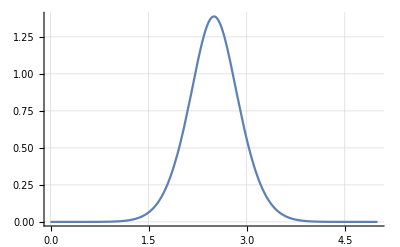
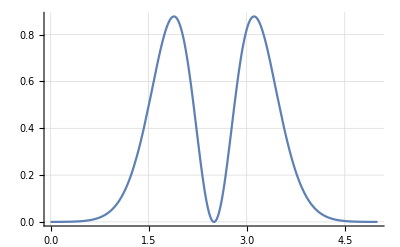
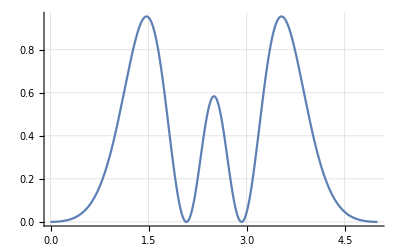
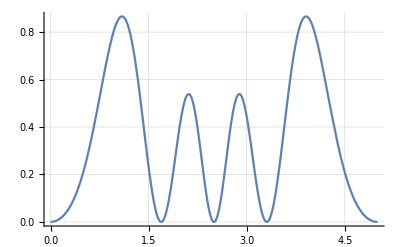
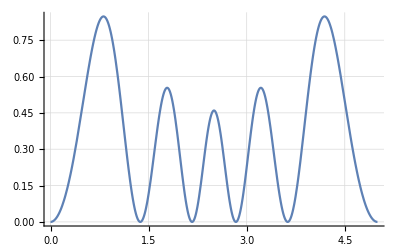
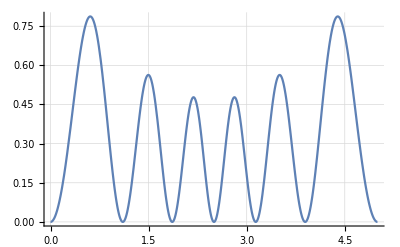

```mathematica
eigvals⟦1;;6⟧
Table[Plot[(Table[-ϕ[x,i,a]vecs⟦j,i⟧,{i,1,nBasis}]//Total)^2,{x,0,a},FrameTicks->Automatic,GridLines->Automatic, PlotRange->All],{j,1,6}]
```

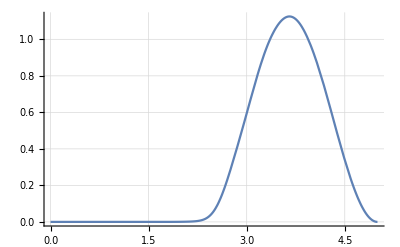
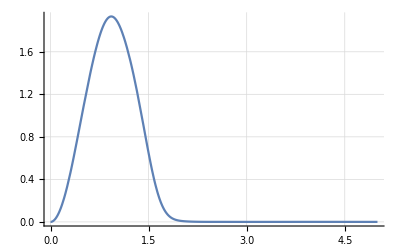
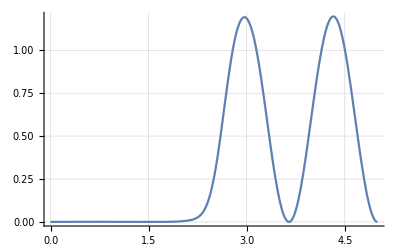
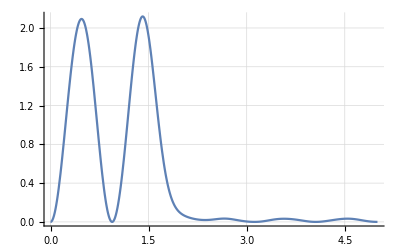
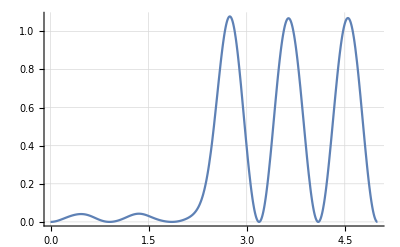
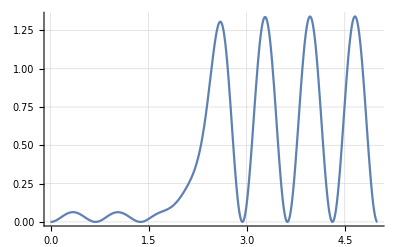
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} (*Problem 1 answer*)
```

## Day 5

(√105)/(√(a^7))

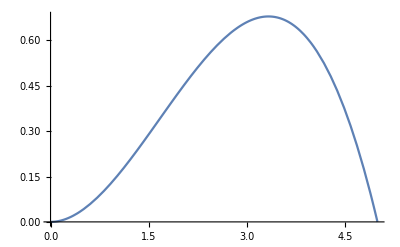

-(2 √210 (1+2 (-1)^n) (1/a)^(7/2) √(a^7))/(n^3 π^3)

(106048101252630746734150722051911982075840900928531888287043246007064912564568 √(a^7) hbar^2)/(205497950578831217572556897801809207623523653949317302866003862855434503975 √105 a^5 m π^2)

```mathematica
$Assumptions=Element[n,Integers];
ψ=x^2(a-x);
A= 1/√Integrate[ψ^2,{x,0,a}]
Plot[(A/.a->5)(ψ/.a->5),{x,0,5}]
c=Integrate[A ψ √(2/a)Sin[(n π x)/a],{x,0,a}]//FullSimplify (*Clearly the a's cancel*)
Integrate[Sum[c (n^2 hbar^2 π^2)/(2 m a^2) √(2/a)Sin[(n π x)/a],{n,100}],{x,0,a}]//FullSimplify (*Mathematica isn't liking to cancel my values out*)
Manipulate[Plot[Re[Sum[(c/.a->5)√(2/5)Sin[(n π x)/5] ⅇ^(-I(n^2 π^2)/(2*5^2)t),{n,10}]]^2+Im[Sum[(c/.a->5)√(2/5)Sin[(n π x)/5] ⅇ^(-I(n^2 π^2)/(2*5^2)t),{n,10}]]^2,{x,0,5}],{t,0,5}]
```